```mathematica
ϕ[t_,θ_]:=Exp[1-(t^(1/θ))];
```

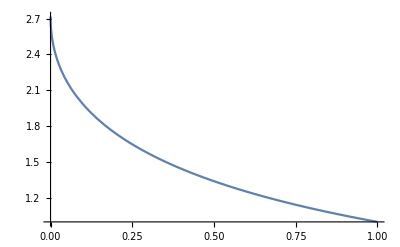

```mathematica
Plot[ϕ[t,2], {t,0,1}]
```

```mathematica
ψ[t_,θ_]:=(1-Log[t])^θ
```

```mathematica
Simplify[ψ[ϕ[t,θ],θ], t>0&&θ>1]
```

t

```mathematica
Simplify[ψ[ϕ[u,θ]+ϕ[v,θ],θ]]
```

(1-Log[ⅇ (ⅇ^(-u^(1/θ))+ⅇ^(-v^(1/θ)))])^θ

```mathematica
Clear[θ,ϕ,ψ]
```

```mathematica
ϕ[t_,θ_]:=-(Log[t])^θ
```

```mathematica
ψ[t_,θ_]:=Exp[-t^(1/θ)]
```

```mathematica
ψ[ϕ[t,θ],θ]
```

ⅇ^(-(-Log[t]^θ)^(1/θ))

```mathematica
Simplify[ψ[ϕ[t,θ],θ], t>0&&θ==1]
```

t

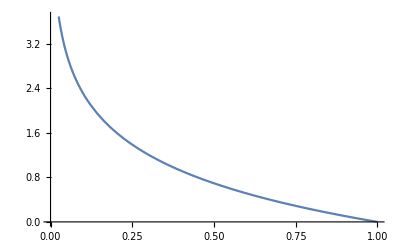

```mathematica
Plot[ϕ[t,1], {t,0,1}]
```